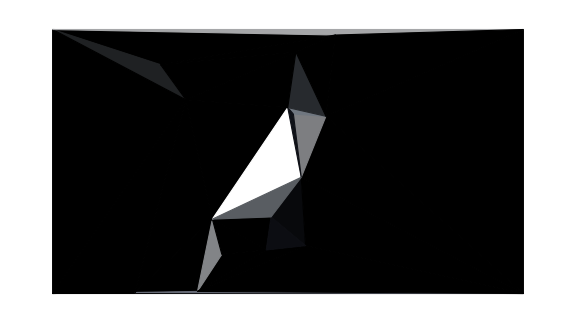

```mathematica
i=Import["/Users/rburke/Documents/\ /tes1.png"];
n=15;
{x,y}=ImageDimensions[i];
pts=Reverse/@RandomChoice[Flatten@ImageData@GradientFilter[i,2]->Tuples@{Range[y,1,-1],Range[x]},n];
pts=Join[pts,{{0,0},{x,0},{x,y},{0,y}}];
m=DelaunayMesh@pts;
Graphics[With[{col=RGBColor@ImageValue[i,Mean@@#]},{EdgeForm@col,col,#}]&/@MeshPrimitives[m,2],ImageSize->Large,Method->{"ShrinkWrap"->True}]
```

```mathematica
Export["LPImg_"<>IntegerString[IntegerPart[RandomReal[]*1000000]]<>".png",Show[%,ImageSize->ImageDimensions[i],AspectRatio->Full]]
```

LPImg_370396.png

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["LPImg_145292.png"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["test2a.png"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["test1a.png"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["test1a.png"]]]
```